## QM

### Create States

```mathematica
States=Flatten[Table[Table[{m,n},{n,m+1,L+2}],{m,1,L+2}],{1,2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{7,8},{7,9},{7,10},{7,11},{7,12},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}

```mathematica
Num[{a_,b_}]:=(a-1)/2(2L+4-a)+b-a;
```

```mathematica
Table[Num[States[[n]]],{n,1,M}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66}

```mathematica
OtherRep={States[[All,1]]-1,States[[All,2]]-States[[All,1]]-1,L+2-States[[All,2]]}ᵀ
```

{{0,0,10},{0,1,9},{0,2,8},{0,3,7},{0,4,6},{0,5,5},{0,6,4},{0,7,3},{0,8,2},{0,9,1},{0,10,0},{1,0,9},{1,1,8},{1,2,7},{1,3,6},{1,4,5},{1,5,4},{1,6,3},{1,7,2},{1,8,1},{1,9,0},{2,0,8},{2,1,7},{2,2,6},{2,3,5},{2,4,4},{2,5,3},{2,6,2},{2,7,1},{2,8,0},{3,0,7},{3,1,6},{3,2,5},{3,3,4},{3,4,3},{3,5,2},{3,6,1},{3,7,0},{4,0,6},{4,1,5},{4,2,4},{4,3,3},{4,4,2},{4,5,1},{4,6,0},{5,0,5},{5,1,4},{5,2,3},{5,3,2},{5,4,1},{5,5,0},{6,0,4},{6,1,3},{6,2,2},{6,3,1},{6,4,0},{7,0,3},{7,1,2},{7,2,1},{7,3,0},{8,0,2},{8,1,1},{8,2,0},{9,0,1},{9,1,0},{10,0,0}}

```mathematica
B2S[{a_,b_,c_}]:={a+1,L+2-c};
```

```mathematica
Table[B2S[OtherRep[[n]]],{n,1,M}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{7,8},{7,9},{7,10},{7,11},{7,12},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}

### Create Ham

```mathematica
Ham=Table[0,{M},{M}];
```

```mathematica
Hamdiag=1/2(OtherRep[[All,1]]+OtherRep[[All,3]])-(OtherRep[[All,1]]-OtherRep[[All,3]]);
```

```mathematica
SxSx[{a_,b_,c_}]:={{1/2 Binomial[a,2]/(Binomial[L,a-2]Binomial[L-(a-2),b+2]),{a-2,b+2,c}},
{1/2 Binomial[b,2]/(Binomial[L,b-2]Binomial[L-(b-2),a+2]),{a+2,b-2,c}},
{1/2 Binomial[b,2]/(Binomial[L,b-2]Binomial[L-(b-2),c+2]),{a,b-2,c+2}},
{2 1/2 Binomial[b,2]/(Binomial[L,b-2]Binomial[L-(b-2),c+1]),{a+1,b-2,c+1}},
{1/2 Binomial[c,2]/(Binomial[L,c-2]Binomial[L-(c-2),b+2]),{a,b+2,c-2}},

{1/2(a b)/(Binomial[L,a-1]Binomial[L-(a-1),b]),{a-1,b,c+1}},{1/2(a b+b c)/(Binomial[L,a]Binomial[L-(a),b]),{a,b,c}},{1/2(a c)/(Binomial[L,c-1]Binomial[L-(c-1),b+2]),{a-1,b+2,c-1}},,{1/2 (b c)/(Binomial[L,c-1]Binomial[L-(c-1),b]),{a+1,b,c-1}}};
```

```mathematica
SxSxVec[{a_,b_,c_}]:={{a-2,b+2,c},{a+2,b-2,c},{a,b-2,c+2},{a+1,b-2,c+1},{a,b+2,c-2},{a-1,b,c+1},{a,b,c},{a-1,b+2,c-1},{a+1,b,c-1}};
```

```mathematica
SxSxConst[1][{a_,b_,c_}]:=1/2 Binomial[a,2]/(√(Binomial[L,a-2]Binomial[L-(a-2),b+2]));SxSxConst[2][{a_,b_,c_}]:=1/2 Binomial[b,2]/(√(Binomial[L,b-2]Binomial[L-(b-2),a+2]));SxSxConst[3][{a_,b_,c_}]:=1/2 Binomial[b,2]/(√(Binomial[L,b-2]Binomial[L-(b-2),c+2]));
SxSxConst[4][{a_,b_,c_}]:=2 1/2 Binomial[b,2]/(√(Binomial[L,b-2]Binomial[L-(b-2),c+1]));
SxSxConst[5][{a_,b_,c_}]:=1/2 Binomial[c,2]/(√(Binomial[L,c-2]Binomial[L-(c-2),b+2]));
SxSxConst[6][{a_,b_,c_}]:=1/2(a b)/(√(Binomial[L,a-1]Binomial[L-(a-1),b]));SxSxConst[7][{a_,b_,c_}]:=1/2(a b+b c)/(√(Binomial[L,a]Binomial[L-(a),b]));SxSxConst[8][{a_,b_,c_}]:=1/2(a c)/(√(Binomial[L,c-1]Binomial[L-(c-1),b+2]));SxSxConst[9][{a_,b_,c_}]:=1/2 (b c)/(√(Binomial[L,c-1]Binomial[L-(c-1),b]));
```

```mathematica
SySyConst[1][{a_,b_,c_}]:=-SxSxConst[1][{a,b,c}];
SySyConst[2][{a_,b_,c_}]:=-SxSxConst[2][{a,b,c}];
SySyConst[3][{a_,b_,c_}]:=-SxSxConst[3][{a,b,c}];
SySyConst[4][{a_,b_,c_}]:=SxSxConst[4][{a,b,c}];
SySyConst[5][{a_,b_,c_}]:=-SxSxConst[5][{a,b,c}];
SySyConst[6][{a_,b_,c_}]:=-SxSxConst[6][{a,b,c}];
SySyConst[7][{a_,b_,c_}]:=SxSxConst[7][{a,b,c}];SySyConst[8][{a_,b_,c_}]:=SxSxConst[8][{a,b,c}];
SySyConst[9][{a_,b_,c_}]:=-SxSxConst[9][{a,b,c}];
```

```mathematica
HamSx=Table[0,{M},{M}];
Do[
Do[
Res= SxSxVec[OtherRep[[n]]];
If[Res[[m,1]]>-1&&Res[[m,2]]>-1&&Res[[m,3]]>-1,
index=Num[B2S[Res[[m]]]];
HamSx[[n, index]] =(-Jx SxSxConst[m][OtherRep[[n]]]-Jy SySyConst[m][OtherRep[[n]]])(√(Binomial[L,OtherRep[[n,1]]]Binomial[L-OtherRep[[n,1]],OtherRep[[n,2]]]));
];
,{m,1,9}]
,{n,1,M}]
```

```mathematica
Ham=1.*(HamSx+DiagonalMatrix[Hamdiag]);
```

### Diagonalize, etc.

```mathematica
Timing[{En,ψn}=Eigensystem[Ham];]
```

{0.00888,Null}

```mathematica
ψn=ψnᵀ;
```

### Initial conditions

```mathematica
allup=Table[0,{M}];
allup[[M]]=1;
```

```mathematica
cn=ψn†.allup;
```

### Operator

```mathematica
JzS=DiagonalMatrix[(OtherRep[[All,1]]-OtherRep[[All,3]])];
```

```mathematica
Jz2=DiagonalMatrix[(OtherRep[[All,1]]+OtherRep[[All,3]])];
```

```mathematica
RotJzS=1.*ψn†.JzS.ψn;
```

```mathematica
RotJz2=1.*ψn†.Jz2.ψn;
```

```mathematica
AvgJzS=Table[0,{Nt}];
AvgJz2=Table[0,{Nt}];
Do[
vec=1.*ⅇ^(-ⅈ times[[n]]En)cn;
AvgJzS[[n]]=Re[vec*.RotJzS.vec];
AvgJz2[[n]]=Re[vec*.RotJz2.vec];
,{n,1,Nt}]
```

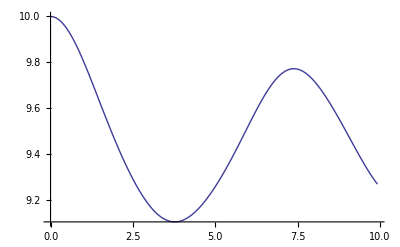

```mathematica
ListPlot[{times,AvgJzS}ᵀ,Joined->True]
```

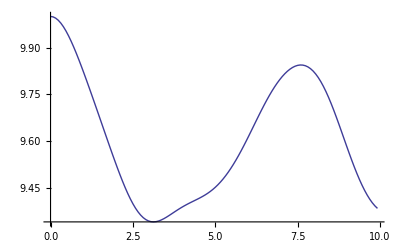

```mathematica
ListPlot[{times,AvgJz2}ᵀ,Joined->True]
```

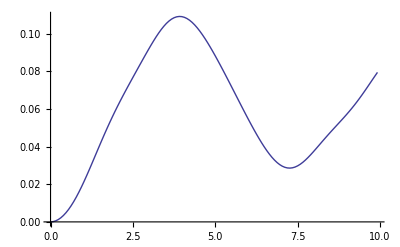

```mathematica
ListPlot[{times,AvgJz2/10-((AvgJzS)/10)^2}ᵀ,Joined->True]
```